```mathematica
(* Jack Farrell, Dept. of Physics, University of Toronto, 2020 *)
(* Investigating the frequency and growth rate of the quasinormal modes of the Dyakonov-Shur Instability of viscous electrons in an annular geometry *)

ClearAll[v0,η,γ,ratio,R1,R2,eq1,eq2,u,n,rawVals];
SetDirectory[NotebookDirectory[]];
ratios = Table[i,{i,0.001,3,0.1}];
freqs=Table[0,{i,1,Length[ratios]}];
rates=Table[0,{i,1,Length[ratios]}];
For[i=1,i<Length[ratios]+1,i++,
v0=0.04;
η=0.01;
γ=0.1;

ratio = ratios[[i]];
R1 = 1/ratio;
R2 = R1+1;

eq1 = D[u[t,r],t] + 2*v0*R2*D[u[t,r]/r,r]+r*D[n[t,r],r] - r*η*(D[u[t,r]/r,{r,2}]+1/r*D[u[t,r]/r, r])==-γ*u[t,r]+NeumannValue[0,r==R1];
eq2 = D[n[t,r],t]+1/r*D[u[t,r],r]==0;

rawVals=NDEigenvalues[{eq1,eq2,DirichletCondition[u[t,r]==0,r==R2],DirichletCondition[n[t,r]==0,r==R1]},{u[t,r],n[t,r]},t,{r,R1,R2},10];
vals=Sort[I*rawVals,Abs[Re[#1]-Pi/2]<Abs[Re[#2]-Pi/2]&];
val=vals[[1]];
freqs[[i]]=Re[val];
rates[[i]]=Im[val];
]
```

```mathematica
freqs
```

{1.56019,1.52818,1.4989,1.47185,1.44667,1.42301,1.40062,1.37925,1.35872,1.33883,1.31942,1.30034,1.28145,1.26262,1.24369,1.22455,1.20504,1.18503,1.16436,1.14287,1.12035,1.09662,1.07144,1.04453,1.01557,0.984186,0.949902,0.912139,0.870148}

```mathematica
rates
```

{0.107114,0.124467,0.142452,0.161066,0.180309,0.200183,0.220692,0.241843,0.263644,0.286107,0.309247,0.333078,0.357621,0.382896,0.408929,0.435747,0.46338,0.491863,0.521234,0.551532,0.582805,0.615101,0.648475,0.682985,0.718696,0.755675,0.793999,0.833747,0.875006}

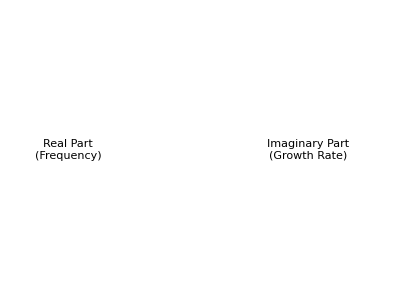

```mathematica
p1=Labeled[Show[ListPlot[Thread[{ratios,freqs}], GridLines->Automatic,PlotStyle->Black], Plot[Pi/2,{x, 0.001, ratios[[Length[ratios]]]}, PlotStyle->Black], PlotRange->All, AxesLabel->{Style[L/Subscript[R, 1], FontWeight->Bold], Style[ω, Bold]}], Style["Real Part
(Frequency)", FontFamily->"Times New Roman"]];
p2=Labeled[Show[ListPlot[Thread[{ratios,rates}],GridLines->Automatic, PlotStyle->Black],Plot[0.106, {x,0,ratios[[Length[ratios]]]}, PlotStyle->Black],AxesLabel->{Style[L/Subscript[R, 1], FontWeight->Bold], Style[ω, Bold]}], Style["Imaginary Part
(Growth Rate)", FontFamily->"Times New Roman"]];
plot1 =GraphicsRow[{p1,p2}]
(*Export["Figures/annular-frequency-growthrate.pdf",plot1]*)
```